```mathematica
nmax = 6;
```

```mathematica
(*spectral problem*)
```

{1.46811,3.49779,5.89759,8.61224,11.6091,14.8655}

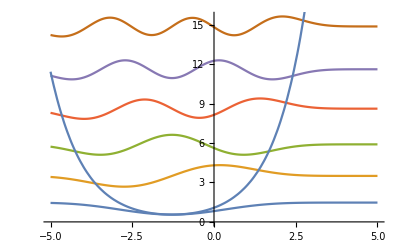

```mathematica
V[x_]:=E^x+Q E^(-x)
h=1.5; 
Q=1/13;
ℒ=-h^2*u''[x]+V[x]*u[x];
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-100,100},nmax,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
vals
Show[Plot[Evaluate[Take[h*funs+vals,nmax]],{x,-5,5}],Plot[V[x],{x,-5,5}]]
```

```mathematica
Subscript[e, n] = Matone relation for NS prepotenial = Q D[W, Q]|_Subscript[a, n]
```

```mathematica
Subscript[a, n]... D[W, a] == 2 π ℏ n  <--> same as Tau zero divisor
```

```mathematica
(*NS prepotential of pure N=2 SU(2) calculated via 4d-blowup*)
```

```mathematica
Subscript[W, inst][a_,ℏ_,q_]:=(q^2 (20 a^2-7 ℏ^2))/(4 ℏ (a^2+ℏ^2) (4 a^2+ℏ^2)^3)+(2 q)/(4 a^2 ℏ+ℏ^3)+(4 q^3 (144 a^4-232 a^2 ℏ^2+29 ℏ^4))/(3 (4 a^2+ℏ^2)^5 (4 a^4 ℏ+13 a^2 ℏ^3+9 ℏ^5));
Subscript[daW, pert] [a_,h_,Q_]:=4 a Log[(Q^(1/4)/h)^2]+2  h I Log[Gamma[1+2  I a /h]/Gamma[1-2 I a /h]]+2π h;
```

```mathematica
Subscript[a, 1] D[W, Subscript[a, 1]] ==2π Subscript[n, 1]
```

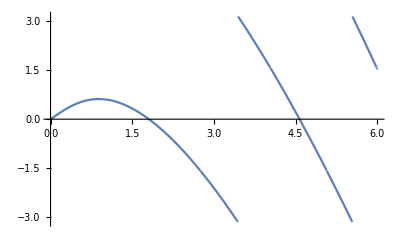

```mathematica
Plot[I Log[Gamma[1+ I a]/Gamma[1- I a]],{a,0,6} ]
```

```mathematica
Options@FindRoots=Sort@Join[Options@FindRoot,{MaxRecursion->Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints->Automatic,Debug->False,ZeroTolerance->10^-2}];

FindRoots[fun_,{var_,min_,max_},opts:OptionsPattern[]]:=Module[{PlotRules,RootRules,g,g2,pts,pts2,lpts,F,sol},(*Extract the Options*)PlotRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@Plot];
RootRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@FindRoot];
(*Plot the function and "mesh" the point with y-coordinate 0*)g=Normal@Plot[fun,{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros*)pts=Cases[g,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
(*Get all plot points*)lpts=Join@@Cases[g,Line[p_]:>SetPrecision[p,OptionValue@WorkingPrecision],Infinity];
(*Derive the interpolated data to find other zeros*)F=InterpolŽation[lpts,InterpolationOrder->2];
g2=Normal@Plot[Evaluate@D[F@var,var],{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros and retain only small ones*)pts2=Cases[g2,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
pts2=Select[pts2,Abs[F@#]<OptionValue@ZeroTolerance&];
pts=Join[pts,pts2];(*Join all zeros*)(*Refine zeros by passing each point through FindRoot*)If[Length@pts>0,pts=Map[FindRoot[fun,{var,#},Evaluate@RootRules]&,pts];
sol=Union@Select[pts,min≤Last@Last@#≤max&];
(*For debug purposes*)If[OptionValue@Debug,Print@Show[g,Graphics@{PointSize@0.02,Red,Point[{var,fun}/.sol]}]];
sol,If[OptionValue@Debug,Print@g];
{}]]
```

```mathematica
Flatten[Table[FindRoots[Re[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a)+(2π h n )],{a,0,nmax}],{n,0,nmax}],1]
```

{{a→1.20435},{a→1.86788},{a→2.93399},{a→2.42735},{a→4.28517},{a→3.85527},{a→4.70017},{a→5.49513},{a→5.8784}}

```mathematica
FindRoots[Re[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a)+(2π h 1 )],{a,1,10}]
```

{{a→1.86788},{a→2.93399}}

```mathematica
a/.avals
```

a

```mathematica
(*avals = Table[FindRoot[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a)+(2π h n ),{a,0},WorkingPrecision->10],{n,0,nmax}]//Quiet;*)
avals = Flatten[Table[FindRoots[Re[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a)+(2π h n )],{a,1,nmax}],{n,0,nmax}],1];
a/.avals
Etable = Table[a^2+(Q D[Subscript[W, inst][a,h,q],q]/.q->Q),{a,a/.avals//Re}]
Show[Plot[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a),{a,0,nmax},Epilog->
Table[InfiniteLine[{Re[(a/.avals)[[n]]],0},{0,1}],{n,0,Length[Etable]}]

],Plot[Evaluate[Table[-2π h n,{n,0,10} ]],{a,0,nmax}]]
```

{1.20435,1.86788,2.93399,2.42735,4.28517,3.85527,4.70017,5.49513,5.8784}

{1.4632,3.49532,8.61112,5.896,18.364,14.8648,22.0928,30.1973,34.5563}

-Graphics-

```mathematica
(*Comparison with Tau zeros*)
```

```mathematica
Show[Plot[Subscript[daW, pert][a,h,Q]+(D[Subscript[W, inst][α,h,Q],α]/.α->a),{a,0,nmax},Epilog->
Table[InfiniteLine[{Re[{1.204,1.8679999999999999,2.427,2.934,3.407,3.8550000000000004}[[n]]],0},{0,1}],{n,0,nmax}]

],Plot[Evaluate[Table[-2π h n,{n,0,10} ]],{a,0,nmax}]]
```

-Graphics-

```mathematica
Table[a^2+(Q D[Subscript[W, inst][a,h,q],q]/.q->Q),{a,{1.204,1.8679999999999999,2.427,2.934,3.407,3.8550000000000004}}]
```

{1.46237,3.49576,5.8943,8.61115,11.6098,14.8627}

```mathematica
{1.4681137399148596,3.497793093523416,5.897585508877191,8.6122423492071,11.6090553704636,14.86546247412721}
```